# Numerisk ekvationslösning

## Exempel 2: Intervallhalveringsmetoden

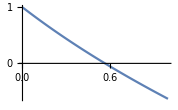

```mathematica
Remove["Global`*"]
f[x_]:=Exp[-x]-x
(* f(x) är strängt avtagande och har max ett nollställe *)
Plot[f[x],{x,0,1}]
```

```mathematica
Remove["Global`*"]
f[x_]:=Exp[-x]-x;
{a,b}={0.55,0.6};
epsilon=0.001;
While[b-a>epsilon,
c=0.5*(a+b);
Print[{a,c,b}];
If[f[a]*f[c]<0,b=c,a=c]
]
(* Kontroll med NSolve *)
NSolve[f[x]==0,x]
```

{0.55,0.575,0.6}

{0.55,0.5625,0.575}

{0.5625,0.56875,0.575}

{0.5625,0.565625,0.56875}

{0.565625,0.567188,0.56875}

{0.565625,0.566406,0.567188}

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→0.567143}}

## Exempel 3: Newton - Raphsons metod

```mathematica
Remove["Global`*"]
f[x_]:=Exp[-x]-x;
epsilon=0.000001;
diff=1;
xold=0.2;
While[diff>epsilon,
xnew=xold-f[xold]/f'[xold];
diff=Abs[xnew-xold];
Print[{xnew,diff}];
xold=xnew;
]
(* Kontroll med NSolve *)
NSolve[f[x]==0,x]
```

{0.540199,0.340199}

{0.567011,0.0268116}

{0.567143,0.000132437}

{0.567143,3.17403×10^-9}

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→0.567143}}

## Exempel 4: Sekantmetoden

```mathematica
Remove["Global`*"]
f[x_]:=Exp[-x]-x;
epsilon=0.000001;
diff=1;
xold=0.2;
xolder=0.1;
While[diff>epsilon,
xnew=xold-f[xold]*(xold-xolder)/(f[xold]-f[xolder]);
diff=Abs[xnew-xold];
Print[{xnew,diff}];
xolder=xold;
xold=xnew;
]
(* Kontroll med NSolve *)
NSolve[f[x]==0,x]
```

{0.53246,0.33246}

{0.564701,0.0322411}

{0.567128,0.0024265}

{0.567143,0.0000154048}

{0.567143,6.81228×10^-9}

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→0.567143}}

## Exempel 5: Fixpunktsiteration

```mathematica
Remove["Global`*"]
f[x_]:=x^3-4x^2+4x+1;
g[1][x_]:=(1/4)*(-x^3+4x^2-1);
g[2][x_]:=-1/(x^2-4x+4);
g[3][x_]:=-(1/2)*Sqrt[x^3+4x+1];
epsilon=0.000001;
diff=1;
For[i=1,i≤3,i++,
xold[i]=-0.2;
k=1;
While[diff>epsilon&&k<30,
xnew[i]=g[i][xold[i]];
diff=Abs[xnew[i]-xold[i]];
xold[i]=xnew[i];
++k
];
diff=1;
]
Print["g[1] = ",g[1][xnew[1]],", g[2] = ",g[2][xnew[2]],", g[3] = ",g[3][xnew[3]]]
(* Kontroll med NSolve *)
NSolve[f[x]==0,x]
```

g[1] = -0.205569, g[2] = -0.205569, g[3] = -0.558467-0.684042 ⅈ

{{x→-0.205569},{x→2.10278-0.665457 ⅈ},{x→2.10278+0.665457 ⅈ}}

```mathematica
Remove["Global`*"]
list={{"k","g1","g2","g3"}};
f[x_]=x^3-4x^2+4x+1;g[x_]={(1/4)*(-x^3+4x^2-1),-1/(x^2-4x+4),-(1/2)*Sqrt[x^3+4x+1]};
kmax=10;
xold=Table[-0.2,{i,1,3}];
For[k=1,k<=kmax,++k,
For[i=1,i≤3,i++,
xnew[i]=g[xold[[i]]][[i]];
xold[[i]]=xnew[i];
];
AppendTo[list,Flatten[{k,Table[DecimalForm[g[xnew[j]][[j]],
DefaultPrintPrecision->10],{j,1,3}]}]]
]
Grid[list,Frame->All]
Print["NSolve: ",NSolve[f[x]==0,x][[1]]]
```

k | g1 | g2 | g3
1 | -0.204486272 | -0.2053753033 | -0.1681722591
2 | -0.2060477348 | -0.2056056223 | -0.2839695103
3 | -0.2053573574 | -0.2055626841 | 0.-0.1992341391 ⅈ
4 | -0.2056632914 | -0.205570688 | -0.5331275146+0.1849998562 ⅈ
5 | -0.2055278555 | -0.205569196 | -0.1901264342-0.5860656233 ⅈ
6 | -0.2055878392 | -0.2055694741 | -0.5783899334+0.4768669252 ⅈ
7 | -0.205561278 | -0.2055694223 | -0.4216500546-0.6752083457 ⅈ
8 | -0.2055730405 | -0.2055694319 | -0.5672817404+0.6066507218 ⅈ
9 | -0.2055678317 | -0.2055694301 | -0.5102962395-0.6831856158 ⅈ
10 | -0.2055701383 | -0.2055694305 | -0.5616549245+0.6560032977 ⅈ

NSolve: {x→-0.205569}

g1'(x) = 1/4 (8 x-3 x^2)

g2'(x) = (-4+2 x)/((4-4 x+x^2)^2)

g3'(x) = -(4+3 x^2)/(4 √(1+4 x+x^3))

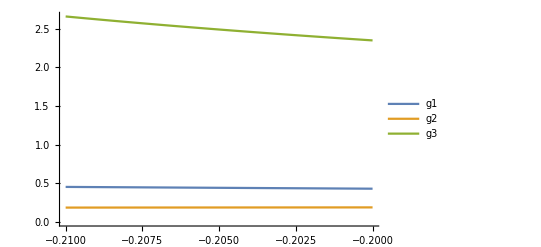

{0.43,{x→-0.2}} | {0.453075,{x→-0.21}}
{0.185291,{x→-0.21}} | {0.187829,{x→-0.2}}
{2.35064,{x→-0.2}} | {2.66084,{x→-0.21}}

```mathematica
Remove["Global`*"]
{xmin,xmax}={-0.21,-0.2};g[x_]={(1/4)*(-x^3+4x^2-1),-1/(x^2-4x+4),-(1/2)*Sqrt[x^3+4x+1]};
Do[Print["g",i,"'(x) = ",g'[x][[i]]],{i,1,3}];
Plot[Evaluate[Table[Abs[g'[x][[i]]],{i,1,3}]],{x,xmin,xmax},PlotLegends->{"g1","g2","g3"}]
Grid[Table[{
FindMinimum[{Abs[g'[x][[i]]],xmin≤x≤xmax},{x,xmin}],FindMaximum[{Abs[g'[x][[i]]],xmin≤x≤xmax},{x,xmin}]
},{i,1,3}],Frame->All]
```